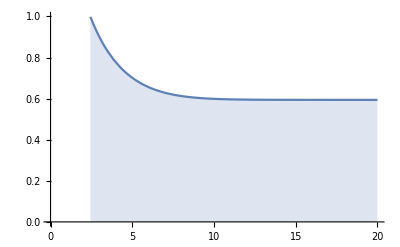

```mathematica
Plot[2.43148(NIntegrate[x^2/(Exp[x]-1),{x,2.43148,y}]/NIntegrate[x^3/(Exp[x]-1),{x,2.43148,y}]),{y, 2.44, 20},PlotRange->{{0.0,20},{0.0,1.5}},Filling->Bottom]
```

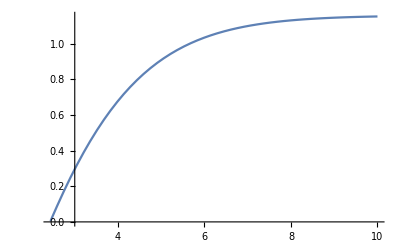

```mathematica
Plot[NIntegrate[x^2/(Exp[x]-1),{x,2.43148,y}],{y, 2.44, 20},PlotRange->{{0.0,20},{0.0,2.0}} ]
```

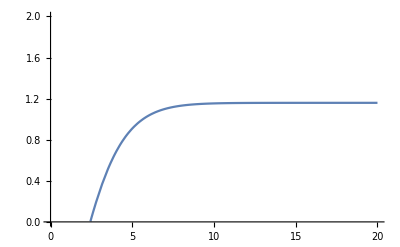

```mathematica
Labeled[Plot[{2.43148(NIntegrate[x^2/(Exp[x]-1),{x,2.43148,y}]/NIntegrate[x^3/(Exp[x]-1),{x,2.43148,y}]),NIntegrate[x^2/(Exp[x]-1),{x,2.43148,y}]/1.163},{y, 2.44, 20},PlotRange->{{0.0,20},{0.0,1.0}}, PlotLegends->Placed[LineLegend[100,{"Efficiency","Normalized power"},LegendFunction->Frame],{{0.8,1.0}}],AxesStyle->{Thick,Thick},TicksStyle->Directive[25],PlotStyle->{Thick}],Style["x_max",30]]
```

-Graphics-x_max

```mathematica
Show[%33,AxesStyle->Black]
```

```mathematica
Plot[{2.43148(NIntegrate[x^2/(Exp[x]-1),{x,2.43148,y}]/NIntegrate[x^3/(Exp[x]-1),{x,2.43148,y}]),NIntegrate[x^2/(Exp[x]-1),{x,2.43148,y}]/1.163},{y, 2.44, 20},PlotRange->{{0.0,20},{0.0,1.0}}, PlotLegends->Placed[LineLegend[100,{"Efficiency","Normalized power"},LegendFunction->Frame],{{0.8,1.0}}],AxesStyle->{Thick,Thick},AxesLabel->{Style["x_max",Large, Bold]},TicksStyle->Directive[25],PlotStyle->{Thick}]
```

-Graphics-

```mathematica
Plot[(y/0.5066)*(NIntegrate[x^2/(Exp[x]-1),{x,y/0.5066,Infinity}]/NIntegrate[x^3/(Exp[x]-1),{x,0,Infinity}]),{y, 0, 20},PlotRange->{{0.0,5},{0.0,0.5}},Filling->Bottom,AxesLabel->{Style["w_g(eV)",Large, Bold],Style["Efficiency", Large, Bold]},TicksStyle->Directive[25],AxesStyle->{Thick,Thick}]
```

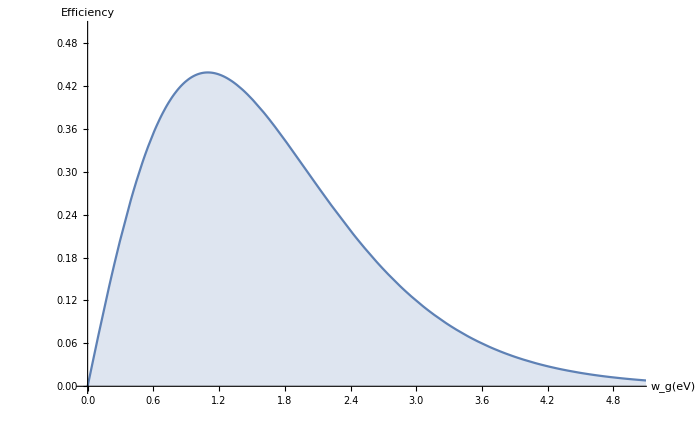
```mathematica
-Graphics-
Plot[(1.1/0.5066)*(NIntegrate[x^2/(Exp[x]-1),{x,1.1/0.5066,y/0.5066}]/NIntegrate[x^3/(Exp[x]-1),{x,0,Infinity}]),{y, 0, 20},PlotRange->{{0.0,5},{0.0,0.5}},Filling->Bottom,AxesLabel->{Style["w_max(eV)",Large, Bold],Style["Efficiency", Large, Bold]},TicksStyle->Directive[25],AxesStyle->{Thick,Thick}]
```

-Graphics-

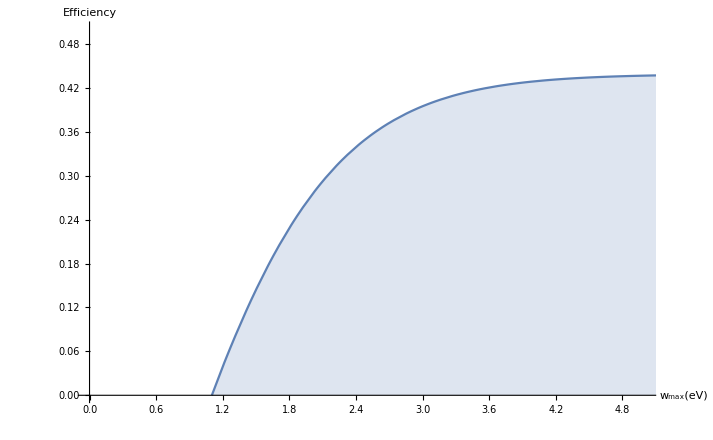

```mathematica
Plot[{(1.1/0.5066)*(NIntegrate[x^2/(Exp[x]-1),{x,1.1/0.5066,y}]/NIntegrate[x^3/(Exp[x]-1),{x,1.1/0.5066,y}]),NIntegrate[x^2/(Exp[x]-1),{x,1.1/0.5066,y}]/NIntegrate[x^2/(Exp[x]-1),{x,1.1/0.5066,Infinity}]},{y, 2.18, 20},PlotRange->{{0.0,10},{0.0,1.0}}, PlotLegends->Placed[LineLegend[100,{"Efficiency","Normalized power"},LegendFunction->Frame],{{0.8,1.0}}],AxesStyle->{Thick,Thick},AxesLabel->{Style["x_max",Large, Bold]},TicksStyle->Directive[25],PlotStyle->{Thick}]
```

-Graphics-

```mathematica
Plot[{(1.1/0.5066)*(NIntegrate[x^2/(Exp[x]-1),{x,1.1/0.5066,y/0.5066}]/NIntegrate[x^3/(Exp[x]-1),{x,1.1/0.5066,y/0.5066}]),NIntegrate[x^2/(Exp[x]-1),{x,1.1/0.5066,y/0.5066}]/NIntegrate[x^2/(Exp[x]-1),{x,1.1/0.5066,Infinity}]},{y, 1.1, 20},PlotRange->{{0.0,10},{0.0,1.0}}, PlotLegends->Placed[LineLegend[100,{"Efficiency","Normalized power"},LegendFunction->Frame],{{0.8,1.0}}],AxesStyle->{Thick,Thick},AxesLabel->{Style["W_max",Large, Bold]},TicksStyle->Directive[25],PlotStyle->{Thick}]
```

-Graphics-

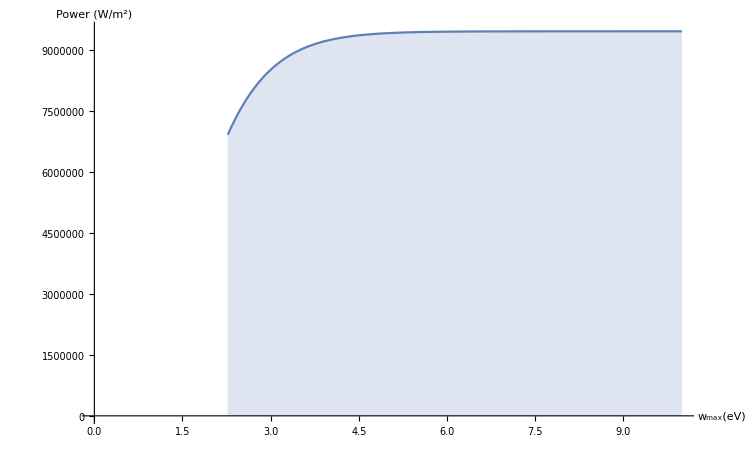

```mathematica
Plot[7.213*(10^6)*NIntegrate[x^2/(Exp[x]-1),{x,1.1/0.5066,y/0.5066}],{y, 1.15/0.5066, 10},PlotRange->{{0.0,10},{0.0, 9.5*10^6}},Filling->Bottom,AxesLabel->{Style["w_max(eV)",Large, Bold],Style["Power (W/m^2)", Large, Bold]},TicksStyle->Directive[25],AxesStyle->{Thick}]
```